```mathematica
(*Data*)
Get["RootSearch`"]
nperiods = 200;
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ = 0;


period = 2 π √(a^3/μ);
ranget = nperiods*period;

psiQ =τ ;


(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});
rp2[t]=rm[t]-({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {0}, {(θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn3 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];
```

```mathematica
motorisedBiffunc[e_]:=(

psi0 = 0;
psidsh0 =0;

r0 = a (1-e);
rdsh0 = 0;

theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,
ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0},
{ψ,θ,rc},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic];
psis[t_]:=ψ[t]/.system[[1]];
psidhs[t_]:=ψ'[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
gammas[t_]:=γ[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
rvs[t_]:=rc'[t]/.system[[1]];

)
```

```mathematica
psistable = {};
Do[Print[e];
motorisedBiffunc[e];
rootst = {};
Do[rootst = Append[rootst,RootSearch[rvs[t]==0,{t,period*n,(n+20)*period}]],
{n,0,nperiods-21,20}];
rootst = Flatten[rootst];
roots = {};
Do[roots = Append[roots,t/.rootst[[n]]],{n,1,Length[rootst]}];
rvals = {};
Do[rvals = Append[rvals,{roots[[n]],rs[roots[[n]]]}],{n,1,Length[roots]}];
peris = Select[rvals,#[[2]]<a&];
psips = {};
Do[psips = Append[psips,{e,psis[peris[[n]][[1]]]}],{n,1,Length[peris]}];
psistable = Append[psistable,psips],
{e,0.01,0.901,0.1}]
ListPlot[psistable]
```

0.01

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision::precset will be suppressed during this calculation.

0.11

0.21

0.31

0.41

0.51

0.61

0.71

0.81

ListPlot::lpn: {{},«7»,{{0.81,0.},{0.81,59.4492},{0.81,200.817},{0.81,292.157},{0.81,417.141},{0.81,506.03},{0.81,563.908},{0.81,688.136},{0.81,736.713},{0.81,794.645},{0.81,942.443},{0.81,1014.72},{0.81,1087.25},{0.81,1230.87},«23»,{0.81,7536.71},{0.81,8244.6},{0.81,8472.44},{0.81,8703.78},{0.81,8935.09},{0.81,9163.16},{0.81,9396.18},{0.81,9631.27},{0.81,10111.8},{0.81,10356.2},{0.81,10842.},{0.81,11081.7},{0.81,11555.4},«96»}} is not a list of numbers or pairs of numbers.

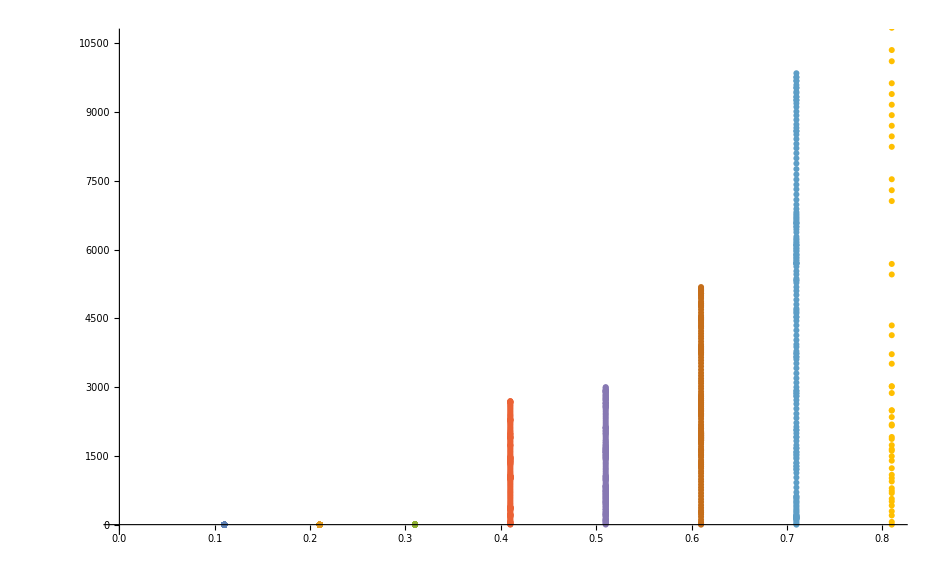

ListPlot::lpn: {{},«8»,{{0.9,971.229},{0.9,1916.33},{0.9,2872.56},{0.9,3178.47},{0.9,3473.15},{0.9,3783.78},{0.9,4108.77},{0.9,5040.41},{0.9,5916.56},{0.9,7175.94},{0.9,7822.6},{0.9,7979.44},{0.9,8658.9},{0.9,10532.},{0.9,12126.7},«22»,{0.9,28441.6},{0.9,29922.5},{0.9,32176.1},{0.9,32496.9},{0.9,32818.2},{0.9,34395.4},{0.9,35598.8},{0.9,35949.8},{0.9,36282.8},{0.9,37463.1},{0.9,38757.3},{0.9,39025.5},{0.9,39682.2},«11»}} is not a list of numbers or pairs of numbers.

```mathematica
ListPlot[psistable[[2;;-1]]]
```

```mathematica
motorisedBiffunc[0.15]
```

```mathematica
rootst = {};
Do[Print[n];rootst = Append[rootst,RootSearch[rvs[t]==0,{t,period*n,(n+20)*period}]],{n,0,nperiods-21,20}];
rootst = Flatten[rootst];
```

0

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

20

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

40

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision::precset will be suppressed during this calculation.

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

880

900

920

940

960

980

1000

1020

1040

1060

1080

1100

1120

1140

1160

1180

1200

1220

1240

1260

1280

1300

1320

1340

1360

1380

1400

1420

1440

1460

1480

1500

1520

1540

1560

1580

1600

1620

1640

1660

1680

1700

1720

1740

1760

1780

1800

1820

1840

1860

1880

1900

1920

1940

1960

1980

2000

2020

2040

2060

2080

2100

2120

2140

2160

2180

2200

2220

2240

2260

2280

2300

2320

2340

2360

```mathematica
roots = {};
Do[roots = Append[roots,t/.rootst[[n]]],{n,1,Length[rootst]}];
rvals = {};
Do[rvals = Append[rvals,{roots[[n]],rs[roots[[n]]]}],{n,1,Length[roots]}]
peris = Select[rvals,#[[2]]<6.6*10^6&];
apos = Select[rvals,#[[2]]>6.6*10^6&];
psips = {};
psias = {};
Do[psips = Append[psips,{psis[peris[[n]][[1]]],psidhs[peris[[n]][[1]]]}],{n,1,Length[peris]}]
Do[psias = Append[psias,{psis[apos[[n]][[1]]],psidhs[apos[[n]][[1]]]}],{n,1,Length[apos]}]
```

2350

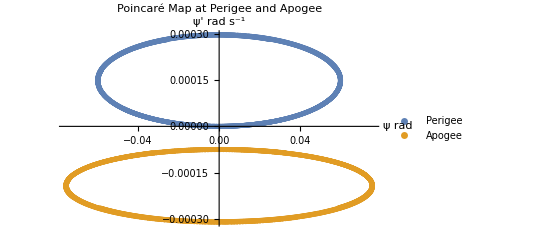

```mathematica
Length[psips]
ListPlot[{psips[[1;;-1]],psias[[1;;-1]]},PlotMarkers->{•,5},PlotLabel->Style["Poincaré Map at Perigee and Apogee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["ψ rad",FontFamily->"Liberation Serif"],Style["ψ' rad s^-1",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotLegends->{"Perigee","Apogee"}]
```